Remark on today's ppt: simply taking pseudo inverse doesnt work (S^+.S !=I)

Y == S.X 
S^+.Y == S^+.S.X
S^+.Y != I.X -> because k<n  i.e. underdetermined system

```mathematica
(S = DiscreteHadamardTransform/@IdentityMatrix[4][[1;;3]])//MatrixForm
(PseudoInverse[S].S)//MatrixForm
```

(1/2 | 1/2 | 1/2 | 1/2
1/2 | 1/2 | -1/2 | -1/2
1/2 | -1/2 | -1/2 | 1/2)

(3/4 | 1/4 | -1/4 | 1/4
1/4 | 3/4 | 1/4 | -1/4
-1/4 | 1/4 | 3/4 | 1/4
1/4 | -1/4 | 1/4 | 3/4)

instead: Y = (S.H^-1).(H.X) -> 
	and take (S.H^-1)_k == rows of I[n,n], where (H.X)_k != 0,
	i.e. raster scanning in the hadamard space.
then the system is determined,and we can take normal inverse.

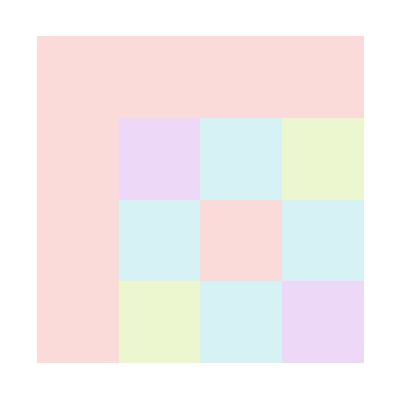
{-Graphics-,-Graphics-}

True

```mathematica
(* checking F^-1 == F^* *)
(F = Fourier/@IdentityMatrix[4])//MatrixForm;
ComplexArrayPlot/@{ConjugateTranspose[F],Inverse[F]}
ConjugateTranspose[F]==Inverse[F]
```

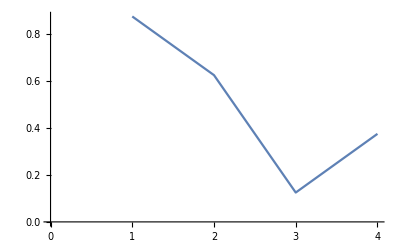
{{7/8,5/8,1/8,3/8},-Graphics-}

```mathematica
(* assume X is 1D signal *)
(X = DiscreteHadamardTransform[{1,1/2,1/4,0}])//{#,ListLinePlot@#}&
```

```mathematica
(* 4 camera pixels, original model *)
(X = DiscreteHadamardTransform[{1,1/2,1/4,0}])//MatrixForm
(H =DiscreteHadamardTransform/@IdentityMatrix[4])//MatrixForm
(S =DiscreteHadamardTransform/@IdentityMatrix[4][[1;;2]])//MatrixForm
(Y=S.X)//MatrixForm
(rX = PseudoInverse[S].Y)// MatrixForm (* seems like illegal here? *)
```

(7/8
5/8
1/8
3/8)

(1/2 | 1/2 | 1/2 | 1/2
1/2 | 1/2 | -1/2 | -1/2
1/2 | -1/2 | -1/2 | 1/2
1/2 | -1/2 | 1/2 | -1/2)

(1/2 | 1/2 | 1/2 | 1/2
1/2 | 1/2 | -1/2 | -1/2)

(1
1/2)

(3/4
3/4
1/4
1/4)

```mathematica
(* 4 camera pixels, near field (no FFT) *)
(X = DiagonalMatrix@DiscreteHadamardTransform[{1,1/2,1/4,0}])//MatrixForm
(S =DiscreteHadamardTransform/@IdentityMatrix[4][[1;;3]])//MatrixForm
```

(7/8 | 0 | 0 | 0
0 | 5/8 | 0 | 0
0 | 0 | 1/8 | 0
0 | 0 | 0 | 3/8)

(1/2 | 1/2 | 1/2 | 1/2
1/2 | 1/2 | -1/2 | -1/2
1/2 | -1/2 | -1/2 | 1/2)

```mathematica
(Y=(S.X)ᵀ)//MatrixForm
(PseudoInverse[S].Yᵀ)//MatrixForm
(rX=(Total/@%ᵀ))//MatrixForm
```

(7/16 | 7/16 | 7/16
5/16 | 5/16 | -5/16
1/16 | -1/16 | -1/16
3/16 | -3/16 | 3/16)

(21/32 | 5/32 | -1/32 | 3/32
7/32 | 15/32 | 1/32 | -3/32
-7/32 | 5/32 | 3/32 | 3/32
7/32 | -5/32 | 1/32 | 9/32)

(7/8
5/8
1/8
3/8)

```mathematica
(* 4 Camera pixels, far field *)
(X =DiagonalMatrix@DiscreteHadamardTransform[{1,1/2,1/4,0}])//MatrixForm
(S =DiscreteHadamardTransform/@IdentityMatrix[4][[1;;4]])//MatrixForm
(F =Fourier/@IdentityMatrix[4])//MatrixForm
```

(7/8 | 0 | 0 | 0
0 | 5/8 | 0 | 0
0 | 0 | 1/8 | 0
0 | 0 | 0 | 3/8)

(1/2 | 1/2 | 1/2 | 1/2
1/2 | 1/2 | -1/2 | -1/2
1/2 | -1/2 | -1/2 | 1/2
1/2 | -1/2 | 1/2 | -1/2)

(0.5 | 0.5 | 0.5 | 0.5
0.5+0. ⅈ | 0.+0.5 ⅈ | -0.5+0. ⅈ | 0.-0.5 ⅈ
0.5 | -0.5 | 0.5 | -0.5
0.5+0. ⅈ | 0.-0.5 ⅈ | -0.5+0. ⅈ | 0.+0.5 ⅈ)

```mathematica
(Y=F.(S.X)ᵀ)//MatrixForm
(PseudoInverse[S].(Inverse[F].Y)ᵀ)//MatrixForm
(rX=Total/@%ᵀ)//MatrixForm
```

(0.5+0. ⅈ | 0.25+0. ⅈ | 0.125+0. ⅈ | 0.+0. ⅈ
0.1875+0.0625 ⅈ | 0.25+0.25 ⅈ | 0.25-0.25 ⅈ | 0.1875-0.0625 ⅈ
0.+0. ⅈ | 0.125+0. ⅈ | 0.25+0. ⅈ | 0.5+0. ⅈ
0.1875-0.0625 ⅈ | 0.25-0.25 ⅈ | 0.25+0.25 ⅈ | 0.1875+0.0625 ⅈ)

(0.875+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.625+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.125+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.375+0. ⅈ)

(0.875+0. ⅈ
0.625+0. ⅈ
0.125+0. ⅈ
0.375+0. ⅈ)

```mathematica
(* Full model I described on today's ppt *)
(* Suppose n = 4, k = 4, m = 2 *)
(* Y = (R.F.(S.X)ᵀ)ᵀ *)
(X = DiagonalMatrix@DiscreteHadamardTransform[{1,1/2,1/4,0}])//MatrixForm
(M = DiscreteHadamardTransform/@IdentityMatrix[4][[1;;4]])//MatrixForm
(F = Fourier/@IdentityMatrix[4])//MatrixForm
(R = ArrayResample[#,{3},"Bin",Resampling->"Linear"]&/@IdentityMatrix[4]//Transpose)//MatrixForm
(Y=(R.F.(M.X)ᵀ)ᵀ)//MatrixForm
(rX = PseudoInverse@M.(PseudoInverse@(R.F).Yᵀ)ᵀ)//MatrixForm//Chop
PseudoInverse[R.F].(R.F)//MatrixForm//Chop
```

(7/8 | 0 | 0 | 0
0 | 5/8 | 0 | 0
0 | 0 | 1/8 | 0
0 | 0 | 0 | 3/8)

(1/2 | 1/2 | 1/2 | 1/2
1/2 | 1/2 | -1/2 | -1/2
1/2 | -1/2 | -1/2 | 1/2
1/2 | -1/2 | 1/2 | -1/2)

(0.5 | 0.5 | 0.5 | 0.5
0.5+0. ⅈ | 0.+0.5 ⅈ | -0.5+0. ⅈ | 0.-0.5 ⅈ
0.5 | -0.5 | 0.5 | -0.5
0.5+0. ⅈ | 0.-0.5 ⅈ | -0.5+0. ⅈ | 0.+0.5 ⅈ)

(5/6 | 1/6 | 0 | 0
0 | 1/2 | 1/2 | 0
0 | 0 | 1/6 | 5/6)

(0.447917+0.0104167 ⅈ | 0.09375+0.03125 ⅈ | 0.15625-0.0520833 ⅈ
0.25+0.0416667 ⅈ | 0.1875+0.125 ⅈ | 0.229167-0.208333 ⅈ
0.145833-0.0416667 ⅈ | 0.25-0.125 ⅈ | 0.25+0.208333 ⅈ
0.03125-0.0104167 ⅈ | 0.34375-0.03125 ⅈ | 0.239583+0.0520833 ⅈ)

(0.875 | 0 | 0 | 0
0 | 0.528846 | 0.144231+0.144231 ⅈ | 0.-0.0961538 ⅈ
0 | 0.0288462-0.0288462 ⅈ | 0.0384615 | 0.0288462+0.0288462 ⅈ
0 | 0.+0.0576923 ⅈ | 0.0865385-0.0865385 ⅈ | 0.317308)

(0.875 | 0 | 0 | 0
0 | 0.528846 | 0.144231+0.144231 ⅈ | 0.-0.0961538 ⅈ
0 | 0.0288462-0.0288462 ⅈ | 0.0384615 | 0.0288462+0.0288462 ⅈ
0 | 0.+0.0576923 ⅈ | 0.0865385-0.0865385 ⅈ | 0.317308)

(1. | 0 | 0 | 0
0 | 0.846154 | 0.230769-0.230769 ⅈ | 0.+0.153846 ⅈ
0 | 0.230769+0.230769 ⅈ | 0.307692 | 0.230769-0.230769 ⅈ
0 | 0.-0.153846 ⅈ | 0.230769+0.230769 ⅈ | 0.846154)

```mathematica
(ConjugateTranspose[F].PseudoInverse[R].Yᵀ)//MatrixForm
(PseudoInverse[S].%ᵀ)//MatrixForm
Total/@(%ᵀ)//MatrixForm
(* reconstruction has bug -> R^+.R != I *)
```

(0.4375+0. ⅈ | 0.4375+0. ⅈ | 0.4375+0. ⅈ | 0.4375+0. ⅈ
0.15625-0.09375 ⅈ | 0.15625+0.09375 ⅈ | -0.15625-0.09375 ⅈ | -0.15625+0.09375 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.09375+0.15625 ⅈ | -0.09375+0.15625 ⅈ | 0.09375-0.15625 ⅈ | -0.09375-0.15625 ⅈ)

(0.875+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.3125+0. ⅈ | 0.+0. ⅈ | 0.+0.3125 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.-0.1875 ⅈ | 0.+0. ⅈ | 0.1875+0. ⅈ)

(0.875+0. ⅈ
0.3125-0.1875 ⅈ
0.+0. ⅈ
0.1875+0.3125 ⅈ)

(0.875
0.625
0.125
0.375)

(5/6 | 1/6 | 0 | 0
0 | 1/2 | 1/2 | 0
0 | 0 | 1/6 | 5/6)

(0.833333+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.0833333+0.0833333 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.25+0.25 ⅈ | 0.25-0.25 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.0833333-0.0833333 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.833333+0. ⅈ
0.+0. ⅈ | 0.0833333-0.0833333 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.25-0.25 ⅈ | 0.25+0.25 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.0833333+0.0833333 ⅈ | 0.+0. ⅈ)

(0.842547+0. ⅈ
0.616225-0.086839 ⅈ
0.118127+0.0764279 ⅈ
0.398058+0. ⅈ)

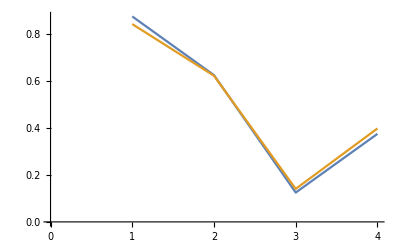

```mathematica
(X = DiscreteHadamardTransform[{1,1/2,1/4,0}])//MatrixForm//N
(R = ArrayResample[#,{3},"Bin",Resampling->"Linear"]&/@IdentityMatrix[4]//Transpose)//MatrixForm
(*(R = ({{1/4, 1/4, 1/4, 1/4}}))//MatrixForm*)
(M = DiscreteHadamardTransform/@IdentityMatrix[4][[1;;4]])//MatrixForm;
(F=Fourier/@IdentityMatrix[4])//MatrixForm;
(S=Outer[Times,F.M,R,1,1]//Flatten[#,1]&)//MatrixForm
(Y=(S.X))//MatrixForm;
(noise = Table[RandomReal[{-0.05,0.05}],{Dimensions[Y][[1]]}]);
(Y= Y+noise)//MatrixForm;
(rX = PseudoInverse@S.Y)//MatrixForm//N
ListLinePlot[{X, Abs@rX}]
```